```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\GitHub\collab-optimizer\data

## Simplified data files from Python sim

```mathematica
tauList=Range[80,120,5];
numRuns=100;
runTime=1000;
SensorNoiseSD={"1.0","2.0","5.0","10.0","20.0","50.0","100.0"};
SignalNoiseSD={"1.0","5.0","15.0","50.0"};
SignalMean=ToString/@tauList;
```

```mathematica
meanCollabRate={tauList,(Mean@Flatten@Import["microsim-theta_1.0-tau_"<>ToString[#]<>"-runtime_1000.txt","Table"]&/@tauList)/(runTime/60)}ᵀ;
meanNoiseCollabRate=Table[{ToExpression[sigmean],Mean@Flatten@Import["noisysim-sigmean_"<>sigmean<>"-signoisesd_"<>signoisesd<>"-sensorsd_"<>sensorsd<>"-runtime_1000.txt","Table"]/(runTime/60)},{sensorsd,SensorNoiseSD},{signoisesd,SignalNoiseSD},{sigmean,SignalMean}];
```

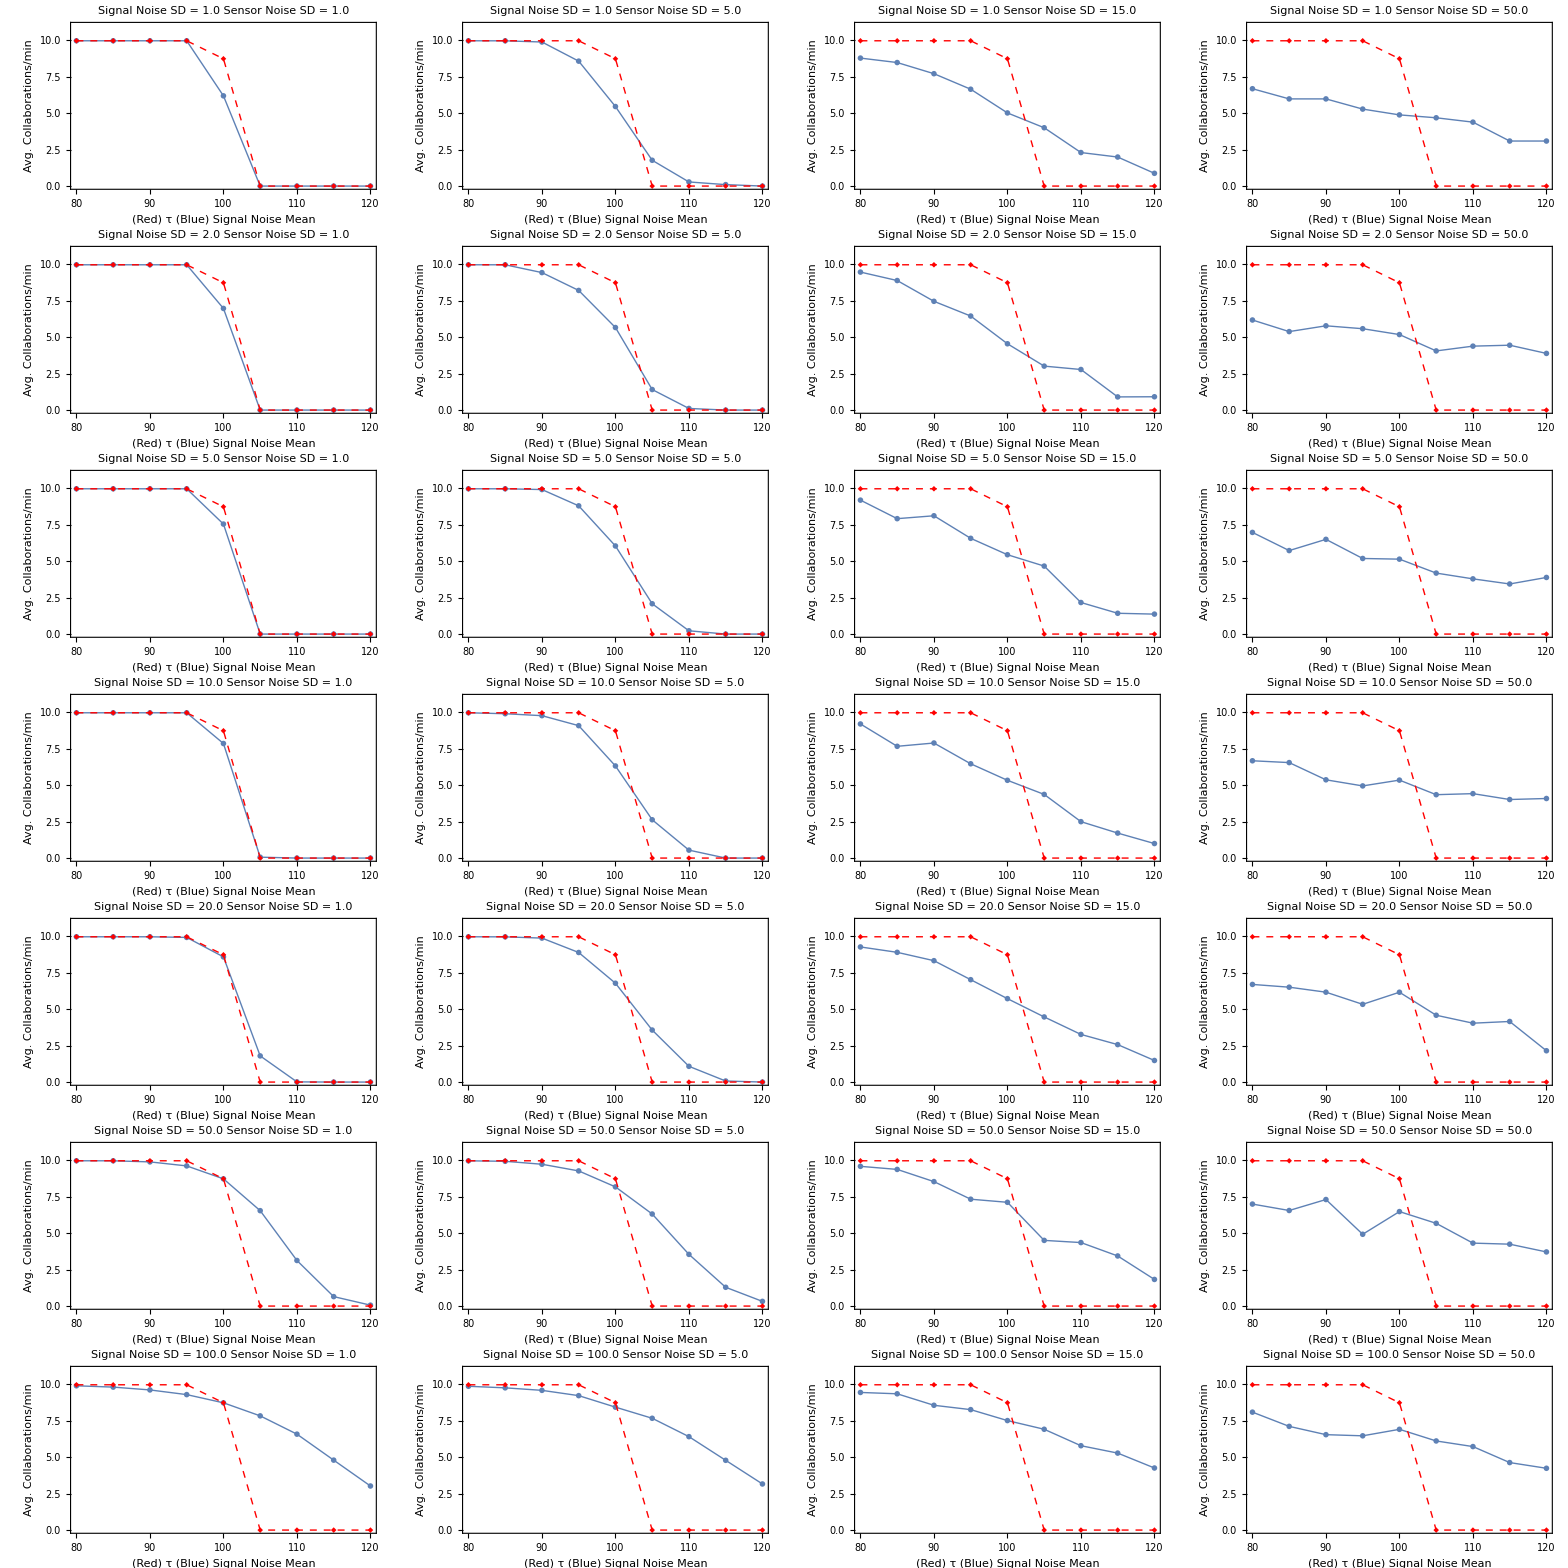

```mathematica
origCollabPlot=ListPlot[meanCollabRate,Joined->True,PlotMarkers->{"◆",Medium},PlotStyle->Directive[Thick,Dashed,Red]];
Table[Show[ListPlot[meanNoiseCollabRate⟦First@First@Position[SensorNoiseSD,sensorsd],First@First@Position[SignalNoiseSD,signoisesd]⟧,Joined->True,PlotMarkers->{Automatic,Medium},PlotStyle->Directive[Thick],Frame->{True,True,False,False},FrameLabel->{"(Red) τ\n(Blue) Signal Noise Mean","Avg. Collaborations/min"},PlotLabel->("Signal Noise SD = "<>sensorsd<>"\nSensor Noise SD = "<>signoisesd),BaseStyle->FontSize->16,PlotRange->{Automatic,{0,11}},ImageSize->{300,300}],origCollabPlot],{sensorsd,SensorNoiseSD},{signoisesd,SignalNoiseSD}]//Grid
```

## Data from real Droplet experiments

```mathematica
AvgRealRunDat[θ_,τ_]:=Module[{dat},
dat[θ,τ]=<<("task_alloc_"<>τ<>"_"<>θ<>".txt");
Length[Select[SplitBy[dat[θ,τ],Last[#]≥4&],MemberQ[Last[Transpose[#]],x_/;x≥ 4]&]]/30]
```

```mathematica
processRealDat=Table[{ToExpression[τ],AvgRealRunDat[θ,τ]},{θ,{"0.1","1.0","10.0"}},{τ,{"2","3","4","5","6"}}]
```

{{{2,139/15},{3,79/10},{4,87/10},{5,259/30},{6,118/15}},{{2,271/30},{3,73/10},{4,76/15},{5,74/15},{6,149/30}},{{2,23/5},{3,37/6},{4,38/5},{5,21/5},{6,21/10}}}

## Overlay data plots

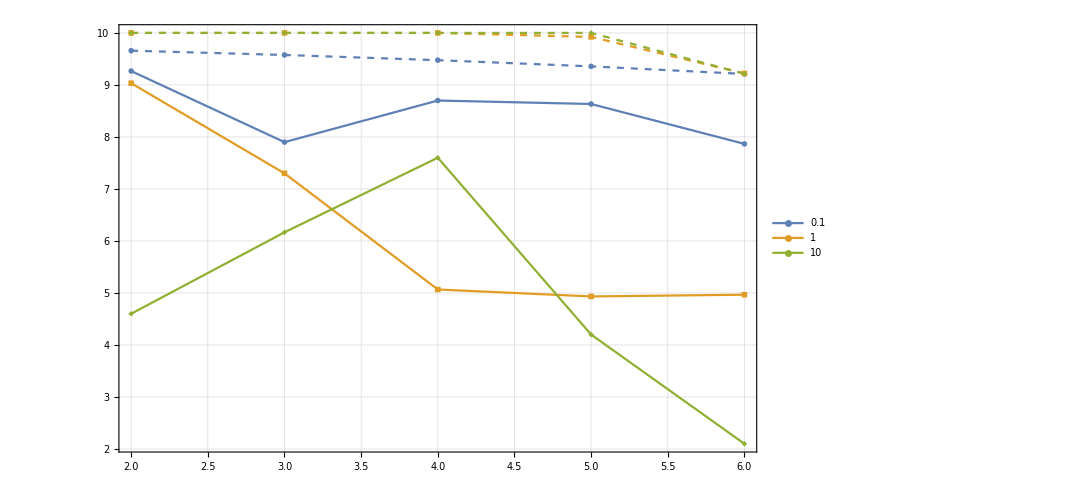

```mathematica
Show[ListPlot[processRealDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick],PlotTheme->"Detailed",ImageSize->800,PlotLegends->{0.1,1,10},PlotRange->{Automatic,{11,2}}],ListPlot[processSimDat,Joined->True,PlotMarkers->{Automatic,Large},PlotStyle->Directive[Thick,Dashed]]]
```